```mathematica
f[x_,y_]:=Piecewise[{{y^2/(2 x), x>0}, {0, x==0&&y==0}}]
```

-Graphics3D-

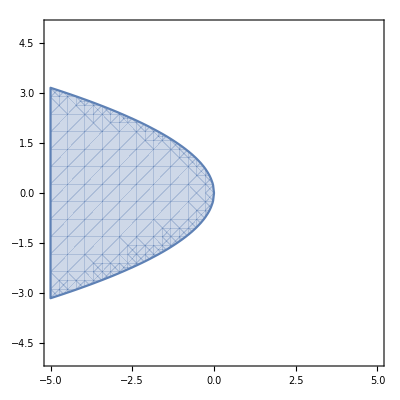

```mathematica
Plot3D[f[x,y],{x,-5,5},{y,-5,5}]
RegionPlot[x+y^2/2≤0,{x,-5,5},{y,-5,5}]
```